```mathematica
raw=Drop[Import[FileNameJoin[{NotebookDirectory[],"data/out.dat"}], "Table", "FieldSeparators"->{" "}, HeaderLines->1], -1];
```

```mathematica
cdata=Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]]}];
vdata=Transpose[{raw[[All, 12]], raw[[All, 13]], raw[[All, 14]]}];
pdata=raw[[All, 16]];
```

```mathematica
arrows=Table[{Arrowheads[.01],Arrow[{
cdata[[i]],cdata[[i]]+
Normalize[vdata[[i]]]*2.0
}]}, {i, Length[raw]}];
```

```mathematica
gg=Graphics3D[arrows,Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large]
```

-Graphics3D-

```mathematica
ListContourPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}], PlotRange->All]
```

-Graphics3D-

```mathematica
ListDensityPlot3D[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 10]], raw[[All, 16]]}],ColorFunction->"TemperatureMap",PlotLegends->Automatic, PlotRange->All]
```

-Graphics3D-

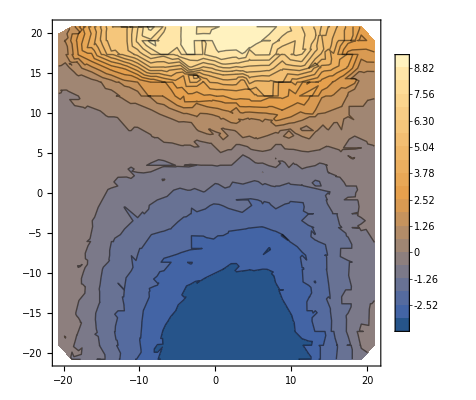

```mathematica
ListContourPlot[Transpose[{raw[[All, 8]], raw[[All, 9]], raw[[All, 12]]}], PlotRange->All, PlotLegends->Automatic, Contours->20]
```

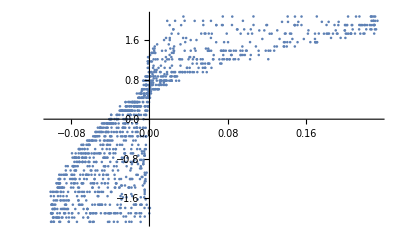

```mathematica
ListPlot[Transpose[{raw[[All, 12]]/40.0, raw[[All, 9]]/10.0}], PlotRange->All]
```